```mathematica
(□_□)_□
```

(□_□)_□

-Graphics-

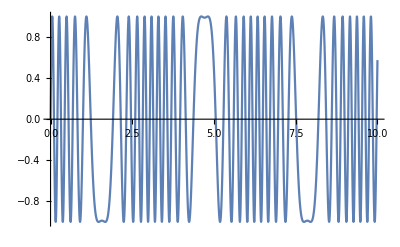

```mathematica
Plot[Sin[30Sin[x]],{x,0,10}]
```

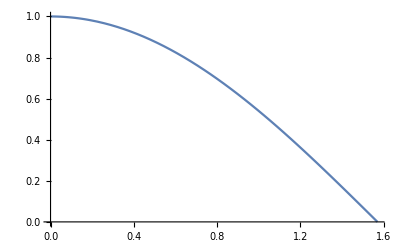

```mathematica
Plot[Cos[x],{x,0,Pi/2}](*fonction décroissante*)
```

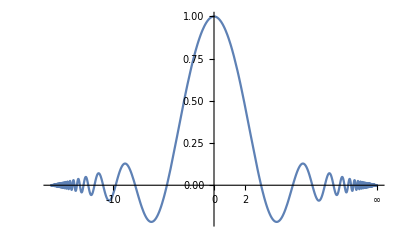

```mathematica
Plot[Sinc[x],{x,-Infinity,Infinity}]
```

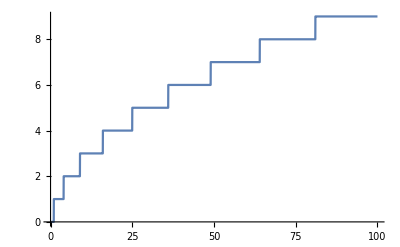

```mathematica
Plot[Floor[Sqrt[x]],{x,0,100}]
```

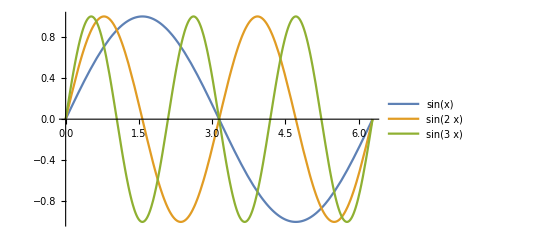

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi},PlotLegends->"Expressions"]
```

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2Pi},PlotLabels->"Expressions"]
```

-Graphics-

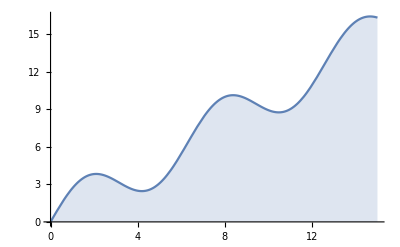

```mathematica
Plot[2Sin[x]+x,{x,0,15},Filling->Bottom]
```

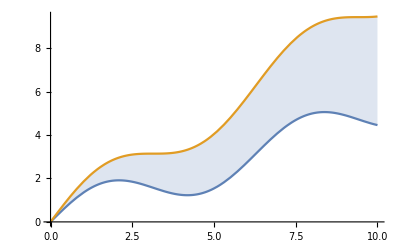

```mathematica
Plot[{Sin[x]+x/2,Sin[x]+x}, {x, 0, 10},Filling->{1->{2}}]
```

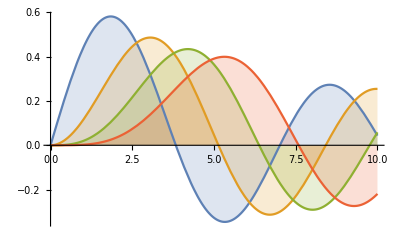

```mathematica
Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis]
```

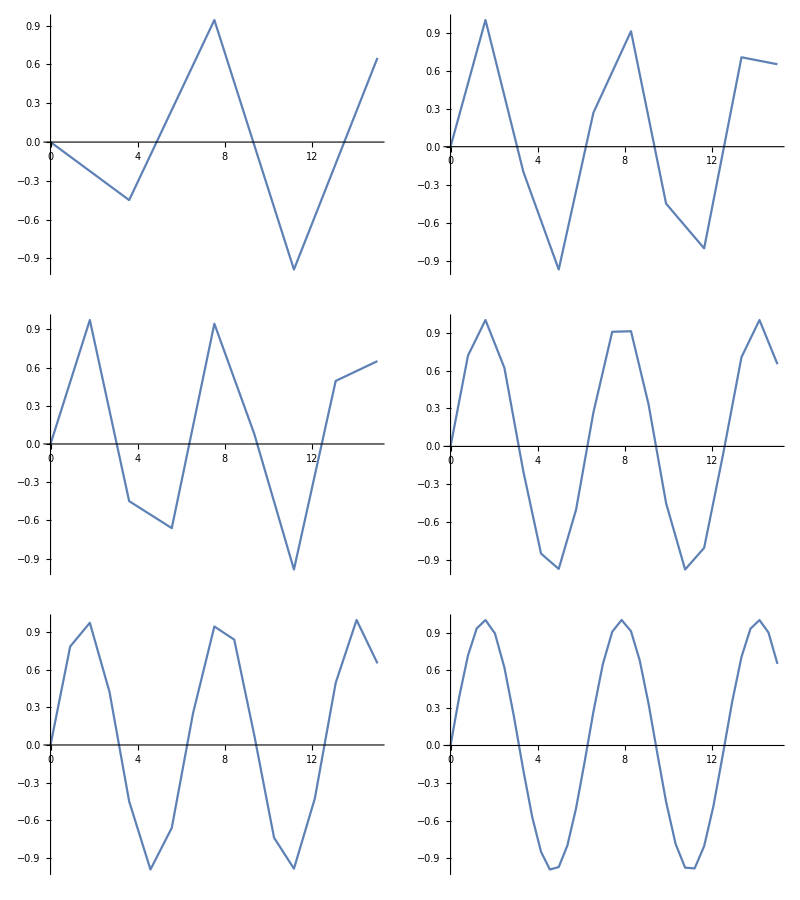

```mathematica
Grid@Table[Plot[Sin[x],{x,0,15},PlotPoints->pp,MaxRecursion->mr],{mr,{0,1,2}},{pp,{5,10}}]
```

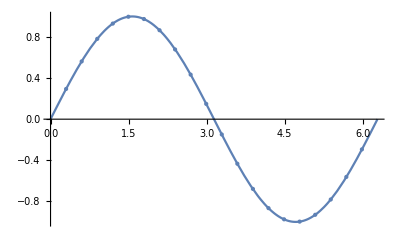

```mathematica
Plot[Sin[x],{x,0,2Pi},Mesh->20]
```

```mathematica
Plot[{BesselJ[0,x],BesselJ[1,x],BesselJ[2,x],BesselJ[3,x],BesselJ[4,x],BesselJ[5,x]},{x,-20,20},PlotLayout->{"Row",2}]
```

-Graphics-

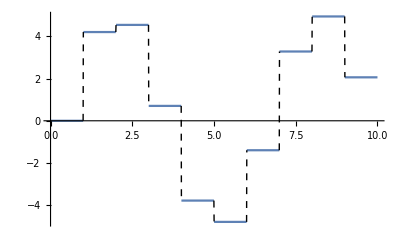

```mathematica
Plot[5Sin[Floor[x]],{x,0,10},Exclusions->{Sin[π x]==0},ExclusionsStyle->Dashed]
```

```mathematica
Plot[{Sin[x],ArcSin[x],x},{x,-π/2,π/2},PlotRange->1.7,PlotStyle->{Red,Green,Dashed}, AspectRatio->Automatic,PlotLabels->"Expressions"]
```

-Graphics-

```mathematica
Plot[{Tan[x],ArcTan[x],x},{x,-Pi/2,Pi/2},PlotRange->Pi,PlotStyle->{Red,Green,Dashed}, AspectRatio->Automatic,PlotLabels->"Expressions"]
```

-Graphics-

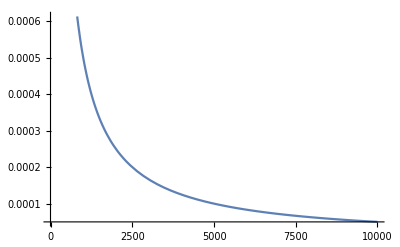

```mathematica
Plot[x-√(x^2-1),{x,1,9999}]
```

```mathematica
S[t]=4/Pi*∑_(p=0)^4 1/(2p+1)*Sin[2*Pi*200*(2p+1)*t]//FullSimplify//Expand
```

(4 Sin[400 π t])/π+(4 Sin[1200 π t])/(3 π)+(4 Sin[2000 π t])/(5 π)+(4 Sin[2800 π t])/(7 π)+(4 Sin[3600 π t])/(9 π)

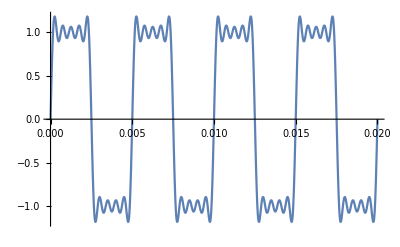

```mathematica
Plot[(4 Sin[400 π t])/π+(4 Sin[1200 π t])/(3 π)+(4 Sin[2000 π t])/(5 π)+(4 Sin[2800 π t])/(7 π)+(4 Sin[3600 π t])/(9 π),{t,0,4/200}]
```

```mathematica
N[%68]
```

%68

```mathematica
S[t_]:=(4 Sin[2400 π t])/(3 π)+(4 Sin[4000 π t])/(5 π)+(4 Sin[5600 π t])/(7 π)+(4 Sin[7200 π t])/(9 π)
```

```mathematica
S[0.0002]
```

0.36733

```mathematica
4/Pi*∑_(p=0)^4 1/(2p+1)*Sin[2*Pi*200*(2p+1)*t]//FullSimplify//Expand
```

(4 Sin[400 π t])/π+(4 Sin[1200 π t])/(3 π)+(4 Sin[2000 π t])/(5 π)+(4 Sin[2800 π t])/(7 π)+(4 Sin[3600 π t])/(9 π)

```mathematica
NMaximize[(4 Sin[400 π t])/π+(4 Sin[1200 π t])/(3 π)+(4 Sin[2000 π t])/(5 π)+(4 Sin[2800 π t])/(7 π)+(4 Sin[3600 π t])/(9 π),{t}]
```

{1.18233,{t→-0.09275}}

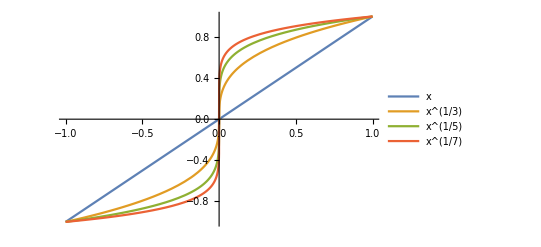

```mathematica
Plot[{x,x^(1/3),x^(1/5),x^(1/7)},{x,-1,1},PlotLegends->"Expressions"]
```